```mathematica
$Assumptions=A∈Reals&&B∈Reals&&ϕ1∈Reals&&ϕ2∈Reals;
```

```mathematica
rho = 1/4*{{1, Exp[I ϕ1]Exp[-B],Exp[I ϕ2]Exp[-B],Exp[I(ϕ1+ϕ2)]Exp[-2B] },{Exp[-I ϕ1 ]Exp[-B], 1, Exp[-I(ϕ1-ϕ2)]Exp[-2B], Exp[I ϕ2]Exp[-B]},{Exp[-I ϕ2]Exp[-B], Exp[I(ϕ1-ϕ2)]Exp[-2B], 1, Exp[I ϕ1]Exp[-B]},{Exp[-I(ϕ1+ϕ2)]Exp[-2B], Exp[-I ϕ2]Exp[-B],Exp[-I ϕ1]Exp[-B], 1}};
MatrixForm[rho]
```

(1/4 | 1/4 ⅇ^(-B+ⅈ ϕ1) | 1/4 ⅇ^(-B+ⅈ ϕ2) | 1/4 ⅇ^(-2 B+ⅈ (ϕ1+ϕ2))
1/4 ⅇ^(-B-ⅈ ϕ1) | 1/4 | 1/4 ⅇ^(-2 B-ⅈ (ϕ1-ϕ2)) | 1/4 ⅇ^(-B+ⅈ ϕ2)
1/4 ⅇ^(-B-ⅈ ϕ2) | 1/4 ⅇ^(-2 B+ⅈ (ϕ1-ϕ2)) | 1/4 | 1/4 ⅇ^(-B+ⅈ ϕ1)
1/4 ⅇ^(-2 B-ⅈ (ϕ1+ϕ2)) | 1/4 ⅇ^(-B-ⅈ ϕ2) | 1/4 ⅇ^(-B-ⅈ ϕ1) | 1/4)

```mathematica
rhoT=1/4*{{1, Exp[-I ϕ1]Exp[-B],Exp[I ϕ2]Exp[-B],Exp[-I(ϕ1-ϕ2)]Exp[-2B] },{Exp[I ϕ1 ]Exp[-B], 1,Exp[-2B], Exp[-I ϕ2]Exp[-B]},{Exp[-I ϕ2]Exp[-B], Exp[-2B], 1, Exp[I ϕ1]Exp[-B]},{Exp[-2B], Exp[I ϕ2]Exp[-B],Exp[-I ϕ1]Exp[-B], 1}} /.ϕ2->ϕ1 ;
MatrixForm[rhoT]
```

(1/4 | 1/4 ⅇ^(-B-ⅈ ϕ1) | 1/4 ⅇ^(-B+ⅈ ϕ1) | ⅇ^(-2 B)/4
1/4 ⅇ^(-B+ⅈ ϕ1) | 1/4 | ⅇ^(-2 B)/4 | 1/4 ⅇ^(-B-ⅈ ϕ1)
1/4 ⅇ^(-B-ⅈ ϕ1) | ⅇ^(-2 B)/4 | 1/4 | 1/4 ⅇ^(-B+ⅈ ϕ1)
ⅇ^(-2 B)/4 | 1/4 ⅇ^(-B+ⅈ ϕ1) | 1/4 ⅇ^(-B-ⅈ ϕ1) | 1/4)

```mathematica
FullSimplify[Eigenvalues[rhoT]]
```

{1/2 ⅇ^-B (-Cos[ϕ1]+Cosh[B]),1/2 ⅇ^-B (Cos[ϕ1]+Cosh[B]),1/4 (1-ⅇ^(-2 B)-2 ⅇ^(-B-ⅈ ϕ1) √(ⅇ^(2 ⅈ ϕ1)) Abs[Sin[ϕ1]]),1/4 (1+ⅇ^(-2 B) (-1+ⅇ^(B-ⅈ ϕ1) √(-(-1+ⅇ^(2 ⅈ ϕ1))^2)))}

```mathematica
eigvals=FullSimplify[Eigenvalues[FullSimplify[rhoT.ConjugateTranspose[rhoT]]]]
```

$Aborted

```mathematica
FullSimplify[Total[Sqrt[eigvals]]]
```

ⅇ^-B (Abs[Sinh[B]]+Cosh[B])

```mathematica
FullSimplify[Sqrt[(-8 ⅇ^(-2 ⅈ A)  ⅇ^(2ⅈ A)Abs[Sin[A]] Abs[Sinh[B]]-2 Cos[2 A]+2 Cosh[2 B])]+Sqrt[(8 ⅇ^(-2 ⅈ A)  ⅇ^(2ⅈ A)Abs[Sin[A]] Abs[Sinh[B]]-2 Cos[2 A]+2 Cosh[2 B])]]
```

2 (Abs[Sin[A]-Sinh[B]]+Abs[Sin[A]+Sinh[B]])

```mathematica
FullSimplify[4 Cosh[B]+2 (Abs[Sin[A]-Sinh[B]]+Abs[Sin[A]+Sinh[B]])]
```

2 (Abs[Sin[A]-Sinh[B]]+Abs[Sin[A]+Sinh[B]]+2 Cosh[B])

```mathematica
FullSimplify[2 (Abs[1-Sinh[B]]+Abs[1+Sinh[B]]+2 Cosh[B])]
```

2 (Abs[-1+Sinh[B]]+Abs[1+Sinh[B]]+2 Cosh[B])

```mathematica
Solve[Log[Exp[-10 x](Cosh[10 x]+1)]==0,x]
```

{{x→ConditionalExpression[1/10 (ⅈ π+2 ⅈ π C[1]+Log[-1+√2]), C[1]∈ℤ]},{x→ConditionalExpression[1/10 (2 ⅈ π C[1]+Log[1+√2]), C[1]∈ℤ]}}

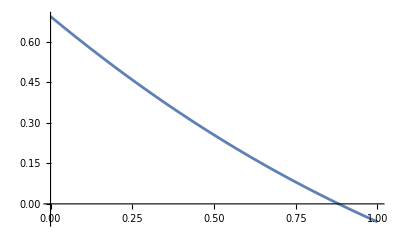

```mathematica
Plot[Log[Exp[-x](Cosh[x]+1)],{x,0,1}]
```

```mathematica
Log[1+Sqrt[2]]//N
```

0.881374

```mathematica
rhoT=1/4*{{1, Exp[-I A],Exp[-I A],Exp[-I 2A] },{Exp[I A ], 1, 1, Exp[-I A]},{Exp[I A], 1, 1, Exp[-I A]},{Exp[I 2A], Exp[I A],Exp[I A], 1}};
MatrixForm[rhoT]
```

(1/4 | ⅇ^(-ⅈ A)/4 | ⅇ^(-ⅈ A)/4 | 1/4 ⅇ^(-2 ⅈ A)
ⅇ^(ⅈ A)/4 | 1/4 | 1/4 | ⅇ^(-ⅈ A)/4
ⅇ^(ⅈ A)/4 | 1/4 | 1/4 | ⅇ^(-ⅈ A)/4
1/4 ⅇ^(2 ⅈ A) | ⅇ^(ⅈ A)/4 | ⅇ^(ⅈ A)/4 | 1/4)

```mathematica
eigvals=FullSimplify[Eigenvalues[rhoT.ConjugateTranspose[rhoT]]]
```

{0,0,0,1}

```mathematica
FullSimplify[Total[Sqrt[eigvals]]]
```

1

```mathematica
rhoTVibr=1/4*{{1,Exp[-I ϕ1]Exp[-A],Exp[I ϕ1]Exp[-A],1}, {Exp[I ϕ1]Exp[-A],1,Exp[-4A],Exp[-I ϕ1]Exp[-A]},{Exp[-I ϕ1]Exp[-A],Exp[-4A],1,Exp[I ϕ1]Exp[-A]},{1,Exp[I ϕ1]Exp[-A],Exp[-I ϕ1]Exp[-A],1}};
MatrixForm[rhoTVibr]
```

(1/4 | 1/4 ⅇ^(-A-ⅈ ϕ1) | 1/4 ⅇ^(-A+ⅈ ϕ1) | 1/4
1/4 ⅇ^(-A+ⅈ ϕ1) | 1/4 | ⅇ^(-4 A)/4 | 1/4 ⅇ^(-A-ⅈ ϕ1)
1/4 ⅇ^(-A-ⅈ ϕ1) | ⅇ^(-4 A)/4 | 1/4 | 1/4 ⅇ^(-A+ⅈ ϕ1)
1/4 | 1/4 ⅇ^(-A+ⅈ ϕ1) | 1/4 ⅇ^(-A-ⅈ ϕ1) | 1/4)

```mathematica
eigValsBetter=FullSimplify[Eigenvalues[rhoTVibr]]
```

{1/8 ⅇ^(-4 A-ⅈ ϕ1) (ⅇ^(ⅈ ϕ1) (1+3 ⅇ^(4 A))-√(4 ⅇ^(6 A)+4 ⅇ^(6 A+4 ⅈ ϕ1)+ⅇ^(2 ⅈ ϕ1) (1-2 ⅇ^(4 A)+8 ⅇ^(6 A)+ⅇ^(8 A)))),1/8 ⅇ^(-4 A-ⅈ ϕ1) (ⅇ^(ⅈ ϕ1) (1+3 ⅇ^(4 A))+√(4 ⅇ^(6 A)+4 ⅇ^(6 A+4 ⅈ ϕ1)+ⅇ^(2 ⅈ ϕ1) (1-2 ⅇ^(4 A)+8 ⅇ^(6 A)+ⅇ^(8 A)))),1/8 ⅇ^(-4 A-ⅈ ϕ1) (ⅇ^(4 A+ⅈ ϕ1)-ⅇ^(ⅈ ϕ1)-√(ⅇ^(2 ⅈ ϕ1) (-1+ⅇ^(4 A))^2-4 ⅇ^(6 A) (-1+ⅇ^(2 ⅈ ϕ1))^2)),1/8 ⅇ^(-4 A-ⅈ ϕ1) (ⅇ^(4 A+ⅈ ϕ1)-ⅇ^(ⅈ ϕ1)+√(ⅇ^(2 ⅈ ϕ1) (-1+ⅇ^(4 A))^2-4 ⅇ^(6 A) (-1+ⅇ^(2 ⅈ ϕ1))^2))}

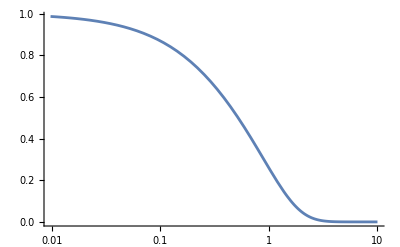

```mathematica
phi=Pi/2;
plottingFunc=Min[Re[eigValsBetter[[3]]/.ϕ1->phi],0];
LogLinearPlot[Log2[2Abs[plottingFunc]+1], {A,0,10}]
```

```mathematica
Expand[ⅇ^(-8 A-2ⅈ ϕ1)(ⅇ^(2 ⅈ ϕ1) (-1+ⅇ^(4 A))^2-4 ⅇ^(6 A) (-1+ⅇ^(2 ⅈ ϕ1))^2)]
```

1+ⅇ^(-8 A)-2 ⅇ^(-4 A)+8 ⅇ^(-2 A)-4 ⅇ^(-2 A-2 ⅈ ϕ1)-4 ⅇ^(-2 A+2 ⅈ ϕ1)

```mathematica
test=1/8(1-ⅇ^(-4 A)-Sqrt[1+ⅇ^(-8 A)-2 ⅇ^(-4 A)+8 ⅇ^(-2 A)-8 ⅇ^(-2 A) Cos[2 ϕ1]]);
LogLinearPlot[Log2[2Abs[test/.ϕ1->phi]+1], {A,0,10}]
```

-Graphics-

```mathematica
FullSimplify[2Abs[test]+1]
```

1/4 ⅇ^(-4 A) (1+3 ⅇ^(4 A)+√((-1+ⅇ^(4 A))^2+16 ⅇ^(6 A) Sin[ϕ1]^2))